# 5. vaja

1. Naloga

```mathematica
v0={10,3}
g=9.81
h=10
x0 = {0,h}
a0 ={0,-g}
```

{10,3}

9.81

10

{0,10}

{0,-9.81}

```mathematica
X[t_] := x0 + v0*t+a0*t^2/2
```

```mathematica
X[2]
```

{20,-3.62}

```mathematica
X[.1]
```

{1.,10.251}

```mathematica
SlikaTocke [t_]:= {PointSize[.03],Point[X[t]]}
```

```mathematica
Graphics[SlikaTocke[1]]
```

-Graphics-

```mathematica
V[t_]:=D[X[x],x]/.x->t
```

```mathematica
V[1]
```

{10,-6.81}

```mathematica
V[t]
```

{10,3-9.81 t}

```mathematica
SlikaVektorja[t_,k_:1]:={Thickness[.005],Arrow[{X[t],X[t]+V[t]*k}]}
```

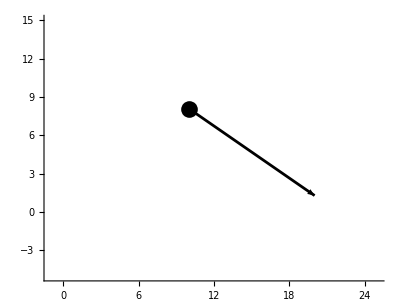

```mathematica
Graphics[{SlikaTocke[1],SlikaVektorja[1]},PlotRange->{{-1,25},{-5,15}},Axes->True,AspectRatio->Automatic]
```

```mathematica
Slika[t_]:=Graphics[{SlikaTocke[t],SlikaVektorja[t]},PlotRange->{{-1,25},{-5,15}},Axes->True,AspectRatio->Automatic]
```

```mathematica
Manipulate[Slika[t],{t,0,5}]
```

```mathematica
casPadca= t /.Solve[X[t][[2]]== 0,t][[2]]
```

1.76604

```mathematica
xPadca=X[casPadca][[1]]
```

17.6604

```mathematica
casNajvisjeTocke=t/.Solve[D[X[t][[2]],t]== 0,t][[1]]
```

0.30581

```mathematica
yNajvisji=X[casNajvisjeTocke][[2]]
```

10.4587

```mathematica
Slika[t_]:=Graphics[{SlikaTocke[t],SlikaVektorja[t,.3]},PlotRange->{{-1,xPadca+4},{-4,yNajvisji+1}},Axes->True,AspectRatio->Automatic]
```

```mathematica
Manipulate[Slika[t],{t,0,casPadca}]
```

```mathematica
Norm[V[casPadca]]
```

17.47

Hitrost, ko žoga pade na tla je 17.47 m/s.

2. naloga

```mathematica
r111 = Ravnina[{-1,-1,-1},{1,1,1}]
```

Ravnina[{-1,-1,-1},{1,1,1}]

```mathematica
SlikaRavnine[Ravnina[n_,v_]]:= Hyperplane[n,v]
```

```mathematica
SlikaRavnine[r111]
```

Hyperplane[{-1,-1,-1},{1,1,1}]

```mathematica
Graphics3D[SlikaRavnine[r111]]
```

-Graphics3D-

```mathematica
Normala[Ravnina[n_,v_]] :=n
Tocka[Ravnina[n_,v_]]:=v

rx=Ravnina[{1,0,0},{0,0,0}]
ry =Ravnina[{0,1,0},{0,0,0}]
rz =Ravnina[{0,0,1},{0,0,0}]
```

Ravnina[{1,0,0},{0,0,0}]

Ravnina[{0,1,0},{0,0,0}]

Ravnina[{0,0,1},{0,0,0}]

```mathematica
Graphics3D@Map[SlikaRavnine,{rx,ry,rz}]
```

-Graphics3D-

```mathematica
SlikaNormale[Ravnina[n_,v_]]:=Arrow[{v,v+n}]
```

```mathematica
SlikaNormale[r111]
```

Arrow[{{1,1,1},{0,0,0}}]

```mathematica
Graphics3D[{SlikaRavnine[r111],SlikaNormale[r111]}]
```

-Graphics3D-

```mathematica
SlikaZNormalo[r_Ravnina]:={SlikaRavnine[r],SlikaNormale[r]}
```

```mathematica
Graphics3D[SlikaZNormalo[rx]]
```

-Graphics3D-

```mathematica
Graphics3D[Map[SlikaZNormalo,{rx,ry,rz,r111}],PlotRange->Automatic]
```

-Graphics3D-

```mathematica
SlikaRavnine
```

```mathematica
Enacba[Ravnina[n_,v_]]:=n[[1]]x+n[[2]]y+n[[3]]z== Total[n.v]
```

```mathematica
Enacba[ry]
```

y==0

```mathematica
ResiSistem[sistem_List]:=Solve[sistem,{x,y,z}]
```

```mathematica
ravnine ={r111,rx,ry,rz}
```

{Ravnina[{-1,-1,-1},{1,1,1}],Ravnina[{1,0,0},{0,0,0}],Ravnina[{0,1,0},{0,0,0}],Ravnina[{0,0,1},{0,0,0}]}

```mathematica
resitveDvojno={x,y,z}/. Map[ResiSistem,Subsets[Map[Enacba,ravnine],{3}]]
```

{{{0,0,3}},{{0,3,0}},{{3,0,0}},{{0,0,0}}}

```mathematica
tocke =Map[First,resitveDvojno]
```

{{0,0,3},{0,3,0},{3,0,0},{0,0,0}}

```mathematica
Presecisca[ravnine_List]:=Module[{resitveDvojno},
resitveDvojno ={x,y,z}/. Map[ResiSistem,Subsets[Map[Enacba,ravnine],{3}]];
Map[First,resitveDvojno]
]
```

```mathematica
Presecisca[ravnine]
```

{{0,0,3},{0,3,0},{3,0,0},{0,0,0}}

```mathematica
SlikaPresecisc[ravnine_List]:= Map[Ball,Presecisca[ravnine]]
Graphics3D[SlikaPresecisc[ravnine]]
```

-Graphics3D-

```mathematica
Slika[ravnine_List]:={Map[SlikaRavnine,ravnine],SlikaPresecisc[ravnine]}
```

```mathematica
Slika[ravnine]
```

{{Hyperplane[{-1,-1,-1},{1,1,1}],Hyperplane[{1,0,0},{0,0,0}],Hyperplane[{0,1,0},{0,0,0}],Hyperplane[{0,0,1},{0,0,0}]},{Ball[{0,0,3}],Ball[{0,3,0}],Ball[{3,0,0}],Ball[{0,0,0}]}}

```mathematica
Graphics3D[Map[SlikaRavnine,ravnine],SlikaPresecisc[ravnine]]
```

-Graphics3D-